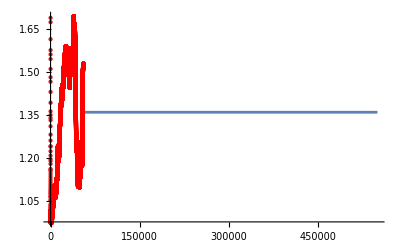

```mathematica
(*============================================================*)
(*1. SETUP:Data Loading and Function Definitions*)
(* ===================================================================*)
(* Read atmospheric 14C data*)
SetDirectory["/Users/yinonmb/Weizmann Institute Dropbox/YinonMoise Bar-On/git/soil_diskin/notebooks"];
C14DATADIR="../data/14C_atm_annot.csv";
C14DATA=Import[C14DATADIR, "HeaderLines"-> 1];
C14DATA= C14DATA[[All,{4,5}]];
(*Interpolate the 14C data, use the mean ratio for extrapolation*)
MeanR = Last[Mean[C14DATA[[-50000;;]]]];
atm14C=Interpolation[C14DATA,InterpolationOrder->0,"ExtrapolationHandler"-> {(MeanR&)}];

(* Plot the results of the interpolation to see it makes sense *)
Plot[atm14C[x],{x,0,550000},Epilog->{PointSize[Medium],Red,Point[C14DATA]}]
```

```mathematica
(* Define the function that calculates the radiocarbon signal from the inputs of the turnover time and mean age of the system *)
LognormalRadiocarbon[tau_,age_] := (
sig = Sqrt[Log[age/tau]];
mu = -Log[Sqrt[tau^3/age]];
r = NIntegrate[ atm14C[a]*Exp[-a/8267]* PDF[LogNormalDistribution[mu,sig],x] * Exp[-x*a] / Exp[-mu+(sig^2)/2],{x,0,Infinity},{a,0,Infinity}, PrecisionGoal->3];
r
)

(* Define the function that optimizes the mean age for a given turnover time and observed radiocarbon signal *)
FindOptimalAge[tau_?NumericQ,rtrue_?NumericQ,InitialAge_?NumericQ]:=(
Module[{objectiveFunction,solution},
(*Define the objective function to minimize:the squared difference between the function output and r_true*)
objectiveFunction[age_?NumericQ]:=(LognormalRadiocarbon[tau,age]-rtrue)^2;
(*Use FindMinimum to find the age that minimizes the objective function*)
(*FindMinimum requires a starting point for'age'*)
solution=Quiet[FindMinimum[objectiveFunction[age],{age,InitialAge}, AccuracyGoal->8, MaxIterations->100]];
(*solution=FindMinimum[objectiveFunction[age],{age,InitialAge}, AccuracyGoal->8, MaxIterations->100];*)
(*Return the value of age that minimizes the difference*)
Return[age/. Last[solution]]]
)
```

```mathematica
(* Run code to optimize all of the site data in parallel *)

(*Ensure parallel kernels are launched (adjust number if needed,0 means all available)*)
LaunchKernels[];

(*3. Distribute definitions to parallel kernels*)
(*Make sure all symbols that FindOptimalAge and LognormalRadiocarbon depend on are distributed.*)
(*atm14C is already defined globally.If it were a more complex structure or function,you'd want to be sure it's available.*)
DistributeDefinitions[LognormalRadiocarbon,FindOptimalAge,atm14C];

(*4. Function to process a single row*)
ProcessRow[{tau_,rtrue_},defaultInitialAge_]:=Module[{optimalAge},Print["Processing: tau = ",tau,", r_true = ",rtrue];
optimalAge=FindOptimalAge[tau,rtrue,defaultInitialAge];
Return[optimalAge];
]
```

LaunchKernels::nodef: Some parallel subkernels are already running. Not launching default kernels again.

```mathematica
(*5. Main script*)
csvFilePath = "../results/tropical_sites_14C_turnover.csv"
Print["Importing data from: ",csvFilePath];
data=Import[csvFilePath,"CSV",HeaderLines->1];
(*data=data[{1},{"turnover","fm"}];*)
defaultInitialAge = 1000;
data = data[[{1,2,3},{7,6}]];
data=Import[csvFilePath,"Dataset",HeaderLines->1];
data = Values[data[[All,{"turnover","fm"}]]]//Normal;
results=ParallelMap[ProcessRow[#,defaultInitialAge]&,data]
```

../results/tropical_sites_14C_turnover.csv

Importing data from: ../results/tropical_sites_14C_turnover.csv

Processing: tau = 10.9002, r_true = 0.911312

Processing: tau = 20.8661, r_true = 0.822271

Processing: tau = 17.7759, r_true = 0.877755

Processing: tau = 17.5075, r_true = 0.889

Processing: tau = 17.4852, r_true = 0.882042

Processing: tau = 34.7018, r_true = 0.995694

Processing: tau = 5.5632, r_true = 0.951472

Processing: tau = 21.6687, r_true = 0.947984

Processing: tau = 11.3855, r_true = 0.894005

Processing: tau = 10.9673, r_true = 0.884773

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

LogNormalDistribution::realprm: Parameter 0.824195-1.5708 ⅈ at position 1 in LogNormalDistribution[0.824195-1.5708 ⅈ,2.84685+0.551766 ⅈ] is expected to be real.

NIntegrate::inumr: The integrand (-0.0461495-5.65168×10^-18 ⅈ) ⅇ^(-a/8267-a x) PDF[LogNormalDistribution[0.824195-1.5708 ⅈ,2.84685+0.551766 ⅈ],x] InterpolatingFunction[{{-13.,55050.}},{5,7,0,{55064},{1},0,0,0,0,MeanR&,«3»},{{-13.,-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,«55054»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«55055»},{1.0193,1.0222,1.02665,1.03017,1.03416,1.03868,1.0515,1.05515,1.0649,1.064,«55054»}},{Automatic}][a] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.},{∞,0.}}.

LogNormalDistribution::realprm: Parameter 0.824195-1.5708 ⅈ at position 1 in LogNormalDistribution[0.824195-1.5708 ⅈ,2.84685+0.551766 ⅈ] is expected to be real.

NIntegrate::inumr: The integrand (-0.0461495-5.65168×10^-18 ⅈ) ⅇ^(-a/8267-a x) PDF[LogNormalDistribution[0.824195-1.5708 ⅈ,2.84685+0.551766 ⅈ],x] InterpolatingFunction[{{-13.,55050.}},{5,7,0,{55064},{1},0,0,0,0,MeanR&,«3»},{{-13.,-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,«55054»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«55055»},{1.0193,1.0222,1.02665,1.03017,1.03416,1.03868,1.0515,1.05515,1.0649,1.064,«55054»}},{Automatic}][a] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.},{∞,0.}}.

LogNormalDistribution::realprm: Parameter 0.824195-1.5708 ⅈ at position 1 in LogNormalDistribution[0.824195-1.5708 ⅈ,2.84685+0.551766 ⅈ] is expected to be real.

General::stop: Further output of LogNormalDistribution::realprm will be suppressed during this calculation.

NIntegrate::inumr: The integrand (-0.0461495-5.65168×10^-18 ⅈ) ⅇ^(-a/8267-a x) PDF[LogNormalDistribution[0.824195-1.5708 ⅈ,2.84685+0.551766 ⅈ],x] InterpolatingFunction[{{-13.,55050.}},{5,7,0,{55064},{1},0,0,0,0,MeanR&,«3»},{{-13.,-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,«55054»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«55055»},{1.0193,1.0222,1.02665,1.03017,1.03416,1.03868,1.0515,1.05515,1.0649,1.064,«55054»}},{Automatic}][a] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.},{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

FindMinimum::nrnum: The function value (-0.947984+NIntegrate[(atm14C[a] Exp[-a/8267] PDF[LogNormalDistribution[mu,sig],x] Exp[«2» a])/Exp[Plus[«2»]],{x,0,∞},{a,0,∞},PrecisionGoal→3])^2 is not a real number at {age} = {-52891.5}.

Processing: tau = 23.8838, r_true = 0.918634

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Processing: tau = 5.61077, r_true = 0.92136

Processing: tau = 11.2605, r_true = 0.922671

LogNormalDistribution::realprm: Parameter 2.11999-1.5708 ⅈ at position 1 in LogNormalDistribution[2.11999-1.5708 ⅈ,3.05722+0.513799 ⅈ] is expected to be real.

NIntegrate::inumr: The integrand (-0.0888061-1.08756×10^-17 ⅈ) ⅇ^(-a/8267-a x) PDF[LogNormalDistribution[2.11999-1.5708 ⅈ,3.05722+0.513799 ⅈ],x] InterpolatingFunction[{{-13.,55050.}},{5,7,0,{55064},{1},0,0,0,0,MeanR&,«3»},{{-13.,-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,«55054»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«55055»},{1.0193,1.0222,1.02665,1.03017,1.03416,1.03868,1.0515,1.05515,1.0649,1.064,«55054»}},{Automatic}][a] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.},{∞,0.}}.

LogNormalDistribution::realprm: Parameter 2.11999-1.5708 ⅈ at position 1 in LogNormalDistribution[2.11999-1.5708 ⅈ,3.05722+0.513799 ⅈ] is expected to be real.

NIntegrate::inumr: The integrand (-0.0888061-1.08756×10^-17 ⅈ) ⅇ^(-a/8267-a x) PDF[LogNormalDistribution[2.11999-1.5708 ⅈ,3.05722+0.513799 ⅈ],x] InterpolatingFunction[{{-13.,55050.}},{5,7,0,{55064},{1},0,0,0,0,MeanR&,«3»},{{-13.,-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,«55054»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«55055»},{1.0193,1.0222,1.02665,1.03017,1.03416,1.03868,1.0515,1.05515,1.0649,1.064,«55054»}},{Automatic}][a] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.},{∞,0.}}.

LogNormalDistribution::realprm: Parameter 2.11999-1.5708 ⅈ at position 1 in LogNormalDistribution[2.11999-1.5708 ⅈ,3.05722+0.513799 ⅈ] is expected to be real.

General::stop: Further output of LogNormalDistribution::realprm will be suppressed during this calculation.

NIntegrate::inumr: The integrand (-0.0888061-1.08756×10^-17 ⅈ) ⅇ^(-a/8267-a x) PDF[LogNormalDistribution[2.11999-1.5708 ⅈ,3.05722+0.513799 ⅈ],x] InterpolatingFunction[{{-13.,55050.}},{5,7,0,{55064},{1},0,0,0,0,MeanR&,«3»},{{-13.,-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,«55054»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«55055»},{1.0193,1.0222,1.02665,1.03017,1.03416,1.03868,1.0515,1.05515,1.0649,1.064,«55054»}},{Automatic}][a] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.},{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

FindMinimum::nrnum: The function value (-0.922671+NIntegrate[(atm14C[a] Exp[-a/8267] PDF[LogNormalDistribution[mu,sig],x] Exp[«2» a])/Exp[Plus[«2»]],{x,0,∞},{a,0,∞},PrecisionGoal→3])^2 is not a real number at {age} = {-99100.}.

Processing: tau = 12.6938, r_true = 0.853911

Processing: tau = 10.6813, r_true = 0.841746

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Processing: tau = 11.7076, r_true = 0.943756

Processing: tau = 34.6131, r_true = 0.995694

Processing: tau = 11.3855, r_true = 0.894005

Processing: tau = 12.2383, r_true = 0.884773

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Processing: tau = 8.98761, r_true = 0.887545

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Processing: tau = 12.4168, r_true = 0.843955

Processing: tau = 15.1828, r_true = 0.889616

Processing: tau = 11.7268, r_true = 0.884773

Processing: tau = 29.2665, r_true = 0.995694

Processing: tau = 11.6565, r_true = 0.853911

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Processing: tau = 7.9129, r_true = 0.844676

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Processing: tau = 9.56115, r_true = 0.939581

Processing: tau = 14.2025, r_true = 0.94198

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Processing: tau = 19.2432, r_true = 0.889

LogNormalDistribution::realprm: Parameter 1.77182-1.5708 ⅈ at position 1 in LogNormalDistribution[1.77182-1.5708 ⅈ,3.0201+0.520114 ⅈ] is expected to be real.

NIntegrate::inumr: The integrand (-0.0704103-8.62277×10^-18 ⅈ) ⅇ^(-a/8267-a x) PDF[LogNormalDistribution[1.77182-1.5708 ⅈ,3.0201+0.520114 ⅈ],x] InterpolatingFunction[{{-13.,55050.}},{5,7,0,{55064},{1},0,0,0,0,MeanR&,«3»},{{-13.,-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,«55054»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«55055»},{1.0193,1.0222,1.02665,1.03017,1.03416,1.03868,1.0515,1.05515,1.0649,1.064,«55054»}},{Automatic}][a] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.},{∞,0.}}.

LogNormalDistribution::realprm: Parameter 1.77182-1.5708 ⅈ at position 1 in LogNormalDistribution[1.77182-1.5708 ⅈ,3.0201+0.520114 ⅈ] is expected to be real.

NIntegrate::inumr: The integrand (-0.0704103-8.62277×10^-18 ⅈ) ⅇ^(-a/8267-a x) PDF[LogNormalDistribution[1.77182-1.5708 ⅈ,3.0201+0.520114 ⅈ],x] InterpolatingFunction[{{-13.,55050.}},{5,7,0,{55064},{1},0,0,0,0,MeanR&,«3»},{{-13.,-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,«55054»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«55055»},{1.0193,1.0222,1.02665,1.03017,1.03416,1.03868,1.0515,1.05515,1.0649,1.064,«55054»}},{Automatic}][a] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.},{∞,0.}}.

LogNormalDistribution::realprm: Parameter 1.77182-1.5708 ⅈ at position 1 in LogNormalDistribution[1.77182-1.5708 ⅈ,3.0201+0.520114 ⅈ] is expected to be real.

General::stop: Further output of LogNormalDistribution::realprm will be suppressed during this calculation.

NIntegrate::inumr: The integrand (-0.0704103-8.62277×10^-18 ⅈ) ⅇ^(-a/8267-a x) PDF[LogNormalDistribution[1.77182-1.5708 ⅈ,3.0201+0.520114 ⅈ],x] InterpolatingFunction[{{-13.,55050.}},{5,7,0,{55064},{1},0,0,0,0,MeanR&,«3»},{{-13.,-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,«55054»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«55055»},{1.0193,1.0222,1.02665,1.03017,1.03416,1.03868,1.0515,1.05515,1.0649,1.064,«55054»}},{Automatic}][a] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.},{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

FindMinimum::nrnum: The function value (-0.94198+NIntegrate[(atm14C[a] Exp[-a/8267] PDF[LogNormalDistribution[mu,sig],x] Exp[«2» a])/Exp[Plus[«2»]],{x,0,∞},{a,0,∞},PrecisionGoal→3])^2 is not a real number at {age} = {-99100.}.

Processing: tau = 10.2181, r_true = 0.94198

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Processing: tau = 6.27878, r_true = 0.894676

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Processing: tau = 10.8831, r_true = 0.850595

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Processing: tau = 14.1328, r_true = 0.871388

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Processing: tau = 9.71448, r_true = 0.893458

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Processing: tau = 13.4429, r_true = 0.822875

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Processing: tau = 6.79786, r_true = 0.953867

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Processing: tau = 6.40464, r_true = 0.894676

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Processing: tau = 3.39555, r_true = 0.853411

LogNormalDistribution::realprm: Parameter 2.87703-1.5708 ⅈ at position 1 in LogNormalDistribution[2.87703-1.5708 ⅈ,3.13657+0.500801 ⅈ] is expected to be real.

Processing: tau = 11.91, r_true = 0.893458

NIntegrate::inumr: The integrand (-0.147105-1.80152×10^-17 ⅈ) ⅇ^(-a/8267-a x) PDF[LogNormalDistribution[2.87703-1.5708 ⅈ,3.13657+0.500801 ⅈ],x] InterpolatingFunction[{{-13.,55050.}},{5,7,0,{55064},{1},0,0,0,0,MeanR&,«3»},{{-13.,-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,«55054»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«55055»},{1.0193,1.0222,1.02665,1.03017,1.03416,1.03868,1.0515,1.05515,1.0649,1.064,«55054»}},{Automatic}][a] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.},{∞,0.}}.

LogNormalDistribution::realprm: Parameter 2.87703-1.5708 ⅈ at position 1 in LogNormalDistribution[2.87703-1.5708 ⅈ,3.13657+0.500801 ⅈ] is expected to be real.

NIntegrate::inumr: The integrand (-0.147105-1.80152×10^-17 ⅈ) ⅇ^(-a/8267-a x) PDF[LogNormalDistribution[2.87703-1.5708 ⅈ,3.13657+0.500801 ⅈ],x] InterpolatingFunction[{{-13.,55050.}},{5,7,0,{55064},{1},0,0,0,0,MeanR&,«3»},{{-13.,-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,«55054»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«55055»},{1.0193,1.0222,1.02665,1.03017,1.03416,1.03868,1.0515,1.05515,1.0649,1.064,«55054»}},{Automatic}][a] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.},{∞,0.}}.

LogNormalDistribution::realprm: Parameter 2.87703-1.5708 ⅈ at position 1 in LogNormalDistribution[2.87703-1.5708 ⅈ,3.13657+0.500801 ⅈ] is expected to be real.

General::stop: Further output of LogNormalDistribution::realprm will be suppressed during this calculation.

NIntegrate::inumr: The integrand (-0.147105-1.80152×10^-17 ⅈ) ⅇ^(-a/8267-a x) PDF[LogNormalDistribution[2.87703-1.5708 ⅈ,3.13657+0.500801 ⅈ],x] InterpolatingFunction[{{-13.,55050.}},{5,7,0,{55064},{1},0,0,0,0,MeanR&,«3»},{{-13.,-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,«55054»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«55055»},{1.0193,1.0222,1.02665,1.03017,1.03416,1.03868,1.0515,1.05515,1.0649,1.064,«55054»}},{Automatic}][a] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.},{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

FindMinimum::nrnum: The function value (-0.953867+NIntegrate[(atm14C[a] Exp[-a/8267] PDF[LogNormalDistribution[mu,sig],x] Exp[«2» a])/Exp[Plus[«2»]],{x,0,∞},{a,0,∞},PrecisionGoal→3])^2 is not a real number at {age} = {-99100.}.

Processing: tau = 7.43038, r_true = 0.953867

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Processing: tau = 9.63614, r_true = 0.894676

$Aborted

```mathematica
(predictions - data[[All, 2]])
```

{4.33833×10^-10,4.68499×10^-10,4.5602×10^-10,4.9158×10^-10,4.69426×10^-10,4.75083×10^-10,4.76433×10^-10,4.33953×10^-10,4.71585×10^-10,4.7262×10^-10,4.48752×10^-10,4.83402×10^-10,5.02797×10^-11,-0.0339769,4.34353×10^-10,4.38067×10^-10,4.37862×10^-10,4.32481×10^-10,-0.0137526,4.19987×10^-10,-0.00894302,-0.0595241,4.73637×10^-10,4.34847×10^-10,4.55161×10^-10,4.55161×10^-10,4.5907×10^-10,4.56656×10^-10,4.60614×10^-10,1.19573×10^-10,8.41882×10^-12,3.21105×10^-10,-0.020017,4.54107×10^-10,4.62358×10^-10,4.08504×10^-10,-0.0368574,4.30912×10^-10,4.34827×10^-10,4.34161×10^-10,4.4897×10^-10,3.43473×10^-10,4.49635×10^-10,4.56973×10^-10,-0.0366116,3.82315×10^-10,4.0501×10^-10,4.12677×10^-10,-0.0432698,-0.00269074,4.76665×10^-10,-0.0581606,-0.0576894,-0.0183142,4.86076×10^-10,4.54732×10^-10,3.43491×10^-10,4.26587×10^-10,6.2321×10^-11,-0.0387723}>1/1000

```mathematica
Length[data[[All,2]]]
```

60

```mathematica
Export["../results/03b_lognormal_model_predictions_14C.csv",predictions,"CSV"]
```

../results/03b_lognormal_model_predictions_14C.csv

```mathematica
Export["../results/03b_lognormal_site_parameters.csv",results,"CSV"]
```

../results/03b_lognormal_site_parameters.csv

```mathematica
CloseKernels[];
```

```mathematica
i= 1;
ModelPrediction[i_]:=Quiet[LognormalRadiocarbon[data[[i,1]],results[[i]]]]

predictions = Map[ModelPrediction,Range[60]];
data[[i,2]]
(*LognormalRadiocarbon[data[[i,1]],85000]*)
results[[i]]
data[[i]];
```

0.911312

11690.4

```mathematica
i = 33;
LognormalRadiocarbon[data[[i,1]],7900]
results[[i]]

(*result=Assuming[{a>0,t>0,b!=0},Integrate[(a * Exp[-x/b])/(a+x),{x,0,t}]]*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.938938

11010.

```mathematica
FindOptimalAge[tau_?NumberQ,rtrue_?NumberQ]:=(
(*Method 2:Using NMinimize to minimize the squared difference*)
(*This method is more robust as it minimizes a cost function and doesn't require the function to be monotonic or have an exact root.*)
Print["Attempting to find optimal age using NMinimize..."];
objectiveFunction[age2_?NumberQ]:=(LognormalRadiocarbon[tau,age2]-rtrue)^2;
(*Set a reasonable search range for'age'.Adjust as needed based on your problem.*)
ageMin=1;
(*Example minimum age*)
ageMax=1000000;
(*Example maximum age*)
optimalAgeNMinimize=NMinimize[objectiveFunction[age],{age,ageMin,ageMax}];
Print["NMinimize Result: ",optimalAgeNMinimize];
optimalAgeNMinimize
)
```

```mathematica
FindOptimalAge[data[[i,1]], data[[i, 2]]]
```

Attempting to find optimal age using NMinimize...

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

LogNormalDistribution::posprm: Parameter 0.+1.09191 ⅈ at position 2 in LogNormalDistribution[-1.8186,0.+1.09191 ⅈ] is expected to be positive.

NIntegrate::inumr: The integrand (0.294503+0. ⅈ) ⅇ^(-a/8267-a x) PDF[LogNormalDistribution[-1.8186,0.+1.09191 ⅈ],x] InterpolatingFunction[{{-13.,55050.}},{5,7,0,{55064},{1},0,0,0,0,MeanR&,«3»},{{-13.,-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,«55054»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«55055»},{1.0193,1.0222,1.02665,1.03017,1.03416,1.03868,1.0515,1.05515,1.0649,1.064,«55054»}},{Automatic}][a] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.},{∞,0.}}.

LogNormalDistribution::posprm: Parameter 0.+1.09191 ⅈ at position 2 in LogNormalDistribution[-1.8186,0.+1.09191 ⅈ] is expected to be positive.

NIntegrate::inumr: The integrand (0.294503+0. ⅈ) ⅇ^(-a/8267-a x) PDF[LogNormalDistribution[-1.8186,0.+1.09191 ⅈ],x] InterpolatingFunction[{{-13.,55050.}},{5,7,0,{55064},{1},0,0,0,0,MeanR&,«3»},{{-13.,-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,«55054»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«55055»},{1.0193,1.0222,1.02665,1.03017,1.03416,1.03868,1.0515,1.05515,1.0649,1.064,«55054»}},{Automatic}][a] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.},{∞,0.}}.

LogNormalDistribution::posprm: Parameter 0.+1.09191 ⅈ at position 2 in LogNormalDistribution[-1.8186,0.+1.09191 ⅈ] is expected to be positive.

General::stop: Further output of LogNormalDistribution::posprm will be suppressed during this calculation.

NIntegrate::inumr: The integrand (0.294503+0. ⅈ) ⅇ^(-a/8267-a x) PDF[LogNormalDistribution[-1.8186,0.+1.09191 ⅈ],x] InterpolatingFunction[{{-13.,55050.}},{5,7,0,{55064},{1},0,0,0,0,MeanR&,«3»},{{-13.,-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,«55054»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«55055»},{1.0193,1.0222,1.02665,1.03017,1.03416,1.03868,1.0515,1.05515,1.0649,1.064,«55054»}},{Automatic}][a] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.},{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NMinimize::nnum: The function value (-0.853411+NIntegrate[(atm14C[a] Exp[-a/8267] PDF[LogNormalDistribution[mu,sig],x] Exp[«2» a])/Exp[Plus[«2»]],{x,0,∞},{a,0,∞},PrecisionGoal→3])^2 is not a number at {age} = {1.03065}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NMinimize::nnum: The function value (-0.853411+NIntegrate[(atm14C[a] Exp[-a/8267] PDF[LogNormalDistribution[mu,sig],x] Exp[«2» a])/Exp[Plus[«2»]],{x,0,∞},{a,0,∞},PrecisionGoal→3])^2 is not a number at {age} = {1.03065}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NMinimize::nnum: The function value (-0.853411+NIntegrate[(atm14C[a] Exp[-a/8267] PDF[LogNormalDistribution[mu,sig],x] Exp[«2» a])/Exp[Plus[«2»]],{x,0,∞},{a,0,∞},PrecisionGoal→3])^2 is not a number at {age} = {1.03065}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

NMinimize Result: NMinimize[objectiveFunction[age],{age,1,1000000}]

NMinimize[objectiveFunction[age],{age,1,1000000}]

```mathematica
D[a * Exp[-x/t] / (a+x) , x]
```

-(a ⅇ^(-x/t))/(a+x)^2-(a ⅇ^(-x/t))/(t (a+x))